```mathematica
TensorData = ToExpression[Import["C:\\ETH\\Neuro\\GlobalTracking\\GlobalTrackingScripts\\tensor_data.txt"]];
dim=Dimensions[TensorData]
Tensor[i_,j_,k_]:={{TensorData[[i,j,k,1]],TensorData[[i,j,k,2]],TensorData[[i,j,k,3]]},{TensorData[[i,j,k,2]],TensorData[[i,j,k,4]],TensorData[[i,j,k,5]]},{TensorData[[i,j,k,3]],TensorData[[i,j,k,5]],TensorData[[i,j,k,6]]}}
```

{9,9,9,6}

### Tensor Visualization

```mathematica
Manipulate[Graphics3D[Table[{ColorFunction->"Rainbow",Ellipsoid[{0.1i,0.1j,0.1k},Tensor[TensorData[[i,j,k,1;;6]]]]},{i,1,dim[[1]]},{j,1,dim[[2]]}]],{k,1,dim[[3]],1}]
```

```mathematica
Graphics3D[Table[{Orange,Specularity[White,20],Opacity[0.5],Ellipsoid[{0.1i,0.1j,0.1k},Tensor[TensorData[[i,j,k,1;;6]]]]},{i,1,dim[[1]]},{j,1,dim[[2]]},{k,1,dim[[3]],1}]]
```

```mathematica
Show[
Table[
ContourPlot3D[{x-i,y-j,z-k}.Inverse[Tensor[TensorData[[3,3,3,1;;6]]]].{x-i,y-j,z-k}==0.25*10^3,{x,-1+i,1+i},{y,-1+j,1+j},{z,-1+k,1+k},
Mesh->None,ContourStyle->Opacity[0.5],ColorFunction->Function[{x,y,z},RGBColor[ArcCos[Eigensystem[Tensor[TensorData[[i,j,k,1;;6]]]][[2,1,1]]]/Pi,ArcCos[Eigensystem[Tensor[TensorData[[i,j,k,1;;6]]]][[2,1,2]]]/Pi,ArcCos[Eigensystem[Tensor[TensorData[[i,j,k,1;;6]]]][[2,1,3]]]/Pi ]]]
,{i,1,dim[[1]],1},{j,1,dim[[2]],1},{k,1,dim[[3]],1}],PlotRange->All]
```

### First Eigendirection

```mathematica
v1[i_,j_,k_]:=Module[{v1},
v1 = Eigensystem[Tensor[i,j,k]][[2,1]];

{Thickness[0.01],RGBColor[ArcCos[v1[[1]]]/Pi,ArcCos[v1[[2]]]/Pi,ArcCos[v1[[3]]]/Pi],Line[{{i,j,k}-v1/2,{i,j,k}+v1/2}]}
]
```

```mathematica
Manipulate[
Graphics3D[
Table[v1[i,j,k],{i,1,dim[[1]]},{j,1,dim[[2]]},{k,1,dim[[3]],1}],
ImageSize->{500,500},ViewPoint->10*{Cos[ϕ],Sin[ϕ],1/2}
],
{ϕ,0,2Pi,2Pi/100},ContentSize ->{0.75*10^3,0.75*10^3},Alignment->Center]
```

```mathematica
Manipulate[
Graphics3D[
Table[v1[i,j,k],{i,1,dim[[1]]},{j,1,dim[[2]]}],
ImageSize->{500,500},ViewPoint->Top
],
{k,1,dim[[3]],1},ContentSize ->{0.75*10^3,0.75*10^3},Alignment->Center]
```

### Spin System

```mathematica
(*
SS[{i_,j_,k_}]:=S[[i,j,k]]

A=Table[{{},{}},{i,1,dim[[1]]},{j,1,dim[[2]]},{k,1,dim[[3]]}];

αmax = Pi/2.;

Eint[i_,j_,k_]:=

If[(A[[i,j,k,1]]=={} || A[[i,j,k,2]]=={})&&(i≠dim[[1]]||i≠dim[[1]]j≠dim[[2]]||j≠dim[[2]]||k≠dim[[3]]||k≠dim[[3]]),

∞,

-0.2*Log[(SS[A[[i,j,k,2]]].({i,j,k}-A[[i,j,k,2]])-Cos[αmax])/(1-Cos[αmax])*(SS[{i,j,k}].({i,j,k}-A[[i,j,k,2]])-Cos[αmax])/(1-Cos[αmax])*(SS[{i,j,k}].(A[[i,j,k,1]]-{i,j,k})-Cos[αmax])/(1-Cos[αmax])*(SS[A[[i,j,k,1]]].(A[[i,j,k,1]]-{i,j,k})-Cos[αmax])/(1-Cos[αmax])*(SS[A[[i,j,k,1]]].SS[A[[i,j,k,2]]]-Cos[αmax])/(1-Cos[αmax])]
]

Eint[i_,j_,k_,ii_,jj_,kk_,str_]:=

If[str == "f",

If[A[[i,j,k,1]]=={},

0.,

If[A[[i,j,k,2]]=={},

-0.2*Log[(SS[{i,j,k}].({ii,jj,kk}-{i,j,k})-Cos[αmax])/(1-Cos[αmax])*(SS[{ii,jj,kk}].({ii,jj,kk}-{i,j,k})-Cos[αmax])/(1-Cos[αmax])]
,

-0.2*Log[(SS[A[[i,j,k,2]]].({i,j,k}-A[[i,j,k,2]])-Cos[αmax])/(1-Cos[αmax])*(SS[{i,j,k}].({i,j,k}-A[[i,j,k,2]])-Cos[αmax])/(1-Cos[αmax])*(SS[{i,j,k}].({ii,jj,kk}-{i,j,k})-Cos[αmax])/(1-Cos[αmax])*(SS[{ii,jj,kk}].({ii,jj,kk}-{i,j,k})-Cos[αmax])/(1-Cos[αmax])*(SS[{ii,jj,kk}].SS[A[[i,j,k,2]]]-Cos[αmax])/(1-Cos[αmax])]
]
],

If[A[[i,j,k,2]]=={},

0.,

If[A[[i,j,k,1]]=={},

-0.2*Log[(SS[{ii,jj,kk}].({i,j,k}-{ii,jj,kk})-Cos[αmax])/(1-Cos[αmax])*(SS[{i,j,k}].({i,j,k}-{ii,jj,kk})-Cos[αmax])/(1-Cos[αmax])]
,

-0.2*Log[(SS[{ii,jj,kk}].({i,j,k}-{ii,jj,kk})-Cos[αmax])/(1-Cos[αmax])*(SS[{i,j,k}].({i,j,k}-{ii,jj,kk})-Cos[αmax])/(1-Cos[αmax])*(SS[{i,j,k}].(A[[i,j,k,1]]-{i,j,k})-Cos[αmax])/(1-Cos[αmax])*(SS[A[[i,j,k,1]]].(A[[i,j,k,1]]-{i,j,k})-Cos[αmax])/(1-Cos[αmax])*(SS[A[[i,j,k,1]]].SS[{ii,jj,kk}]-Cos[αmax])/(1-Cos[αmax])]
]
]
]*)
```

```mathematica
g[{ϕ_,θ_}]:={Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}

S = Table[g[{RandomReal[{0,2Pi}],RandomReal[{0,Pi}]}],{i,1,dim[[1]]},{j,1,dim[[2]]},{k,1,dim[[3]]}];

Ed[i_,j_,k_]:=S[[i,j,k]].Inverse[Tensor[i,j,k]].S[[i,j,k]]

p[i_,j_,k_]:=Exp[-Ed[i,j,k] ]

Etot[S_]:=Sum[Ed[i,j,k],{i,1,dim[[1]]},{j,1,dim[[2]]},{k,1,dim[[3]]}];
```

```mathematica
(*newA[i_,j_,k_,N_]:=Module[{ii,jj,kk},

For[ii=i-N,ii≤i+N,ii++,
For[jj=j-N,jj≤j+N,jj++,
For[kk=k-N,kk≤k+N,kk++,
If[{ii,jj,kk}≠ {i,j,k}&&ii^2+jj^2+kk^2≤N^2,
If[S[[i,j,k]].({ii,jj,kk}-{i,j,k})>0,
If[Eint[i,j,k,ii,jj,kk,"f"]<Eint[i,j,k],
A[[i,j,k,1]]={ii,jj,kk};],
If[Eint[i,j,k,ii,jj,kk,"b"]<Eint[i,j,k],
A[[i,j,k,2]]={ii,jj,kk};]
]
]
]]]
]*)
```

```mathematica
(*MC2[i_,j_,k_]:=Module[{gnew,gold,pnew,pold,pacc},

gold =S[[i,j,k]];
pold = Exp[-Etot[S]];

gnew = g[{RandomReal[{0,2Pi}],RandomReal[{0,Pi}]}];
S[[i,j,k]] = gnew;
pnew= Exp[-Etot[S]];

pacc = Min[1, pnew/pold];

If[RandomReal[]>pacc,S[[i,j,k]] = gold];

]
```

```mathematica
(*MC3[i_,j_,k_]:=Module[{aold,fnew,fold,bnew,bold,pnew,pold,paccf,paccb,Nijk,N=3},

aold =A[[i,j,k]];
pold = Exp[-Etot[S]];

Nijk = Table[{ii,jj,kk},{ii,i-N,i+N},{jj,j-N,j+N},{kk,k-N,k+N}];
Fijk = Select[Nijk,((#-{i,j,k}).S[[i,j,k]]>0 && # ≠ {i,j,k})&];
Bijk = Select[Nijk,((#-{i,j,k}).S[[i,j,k]]<=0 && # ≠ {i,j,k})&];

fnew =RandomChoice[Fijk];
bnew =RandomChoice[Bijk];

A[[i,j,k,1]] = fnew;
A[[i,j,k,2]] = bnew;

pnew= Exp[-Etot[S]];

pacc = Min[1, pnew/pold];

If[RandomReal[]>pacc,S[[i,j,k]] = gold];

]*)
```

```mathematica
MC[i_,j_,k_]:=Module[{gnew,gold,pold,pnew,pacc},

pold =p[i,j,k];
gold = S[[i,j,k]];

gnew = g[{RandomReal[{0,2Pi}],RandomReal[{0,Pi}]}];
S[[i,j,k]]=gnew;
pnew = p[i,j,k];

pacc = Min[1,pnew/pold];

If[RandomReal[]>pacc,S[[i,j,k]] = gold];
]
```

```mathematica
Energy ={};
Block[{i,j,k,n},

For[n=1,n≤100,n++,

Energy = Append[Energy,Etot[S]];

For[i=1,i≤dim[[1]],i++,
For[j=1,j<=dim[[2]],j++,
For[k=1,k<=dim[[3]],k++,
MC[i,j,k];
]]]
];

]
```

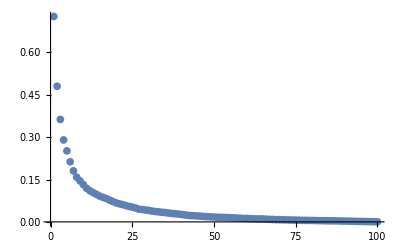

```mathematica
S0= Table[Eigenvectors[Tensor[i,j,k]][[1]],{i,1,dim[[1]]},{j,1,dim[[2]]},{k,1,dim[[3]]}];
E0=Etot[S0];
ListPlot[(Energy-E0)/E0,PlotRange->All]
```